```mathematica
csv=Import["/home/vlad/Desktop/TEMPORARY-GDELT/datavlad.csv"];
```

```mathematica
csv[[2;;,2;;]]//Dimensions
```

{166,10}

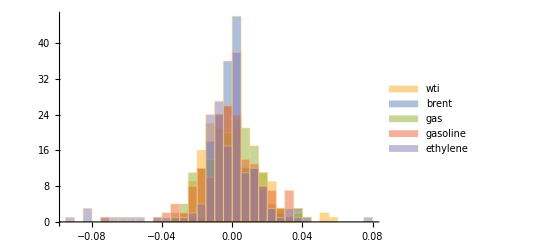

```mathematica
Histogram[csv[[2;;,2;;6]]//Transpose, ChartLegends->csv[[1,2;;6]]]
```

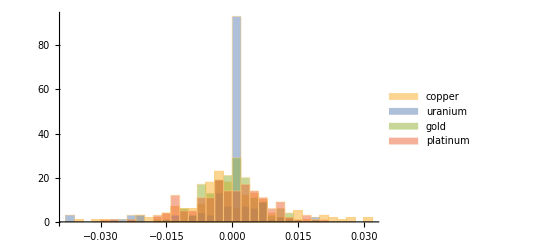

```mathematica
Histogram[csv[[2;;,7;;10]]//Transpose, ChartLegends->First[csv][[7;;10]]]
```